#### Section (iv/v)

Unless otherwise specified, a, b, c, and d are the digits of a number where 9≥a,b,c,d≥0.

Conjecture 1: By applying this routine, 6174 maps to itself. Further, 6174 is the only 4 digit number which maps to itself.

Proof:
6174: 7641-1467=7614.
Now, we prove that this is only possible for 6174.
Our goal is to find a 4-digit integer n which results in n after applying this routine. 

Now, let a,b,c,d be the digits of n. Let 9≥a≥b≥c≥d≥0, though equality cannot hold the whole way across, that is, not all the digits can be the same. Now applying the routine we obtain now we apply the routine to find the new number, 1000a+100b+10c+d-(1000d+100c+10b+a), which we will call ABCD. D=10+d-a because a>d (borrowing from next place). C=10+c-1-b=9+c-b because c≥d (borrowing from next place). B=b-1-c. A=a-d.

Note that because A and D are expressed in terms of a and d, A and D cannot correspond to either. For example, if we let A=a then d=0. This implies that there are infinitely many possibilities for D. So A and D must correspond to b and c, then B and C correspond to a and d. 

If we let B=a then b-1-c=a, or b-c=a+1. However, this must be impossible because a≥b,c. Thus, this leaves B=d implying that C=a.

Trying A=b,B=d,C=a,D=c. This yields:
a-d=b
b-1-c=d
9+c-b=a
10+d-a=c

```mathematica
Solve[a-d==b&&b-1-c==d&&9+c-b==a&&10+d-a==c,{a,b,c,d}]
```

{{a→7,b→6,c→4,d→1}}

Substituting we obtain A=6,B=1,C=7,D=4 so n=6174

To prevent missing any other solutions, we try the other option: A=c,B=d,C=a,D=b. This would yield
a-d=c
b-1-c=d
9+c-b=a
10+d-a=b

```mathematica
Solve[a-d==c&&b-1-c==d&&9+c-b==a&&10+d-a==b,{a,b,c,d}]
```

{{a→17/3,b→20/3,c→10/3,d→7/3}}

This solution clearly does not satisfy the conditions of the problem, so 6174 is the only possible solution for n.

Conjecture 2: All numbers generated by this routine are divisible by 9.

Proof:
Let 9≥a≥b≥c≥d≥0 be the digits of some number to which we will apply Kaprekar’s Routine. Therefore our new number will be:
1000a+100b+10c+d-(1000d+100c+10b+a)
=999a+90b-90c-999d
=9(111a+10b-10c-111d)

Conjecture 3: Applying the routine to two numbers that differ by 1 will result in outcomes that differ by predictable values. More specifically:
If 9>a>b>c>d+1>0 for the digits a,b,c,d of the number, that is the new number abc(d+1) contains no repeated digits, then applying the routine to the numbers abcd and abc(d+1) will result in outcomes which differ by 999. 

Proof:
Let 9>a>b>c>d+1>0 for the digits.Then, the two numbers are 1000a+100b+10c+d and 1000a+100b+10c+d+1. Applying the routine to each:
1000a+100b+10c+d-(1000d+100c+10b+a)=999a+90b-90c-999d
1000a+100b+10c+d+1-(1000(d+1)+100c+10b+a)=999a+90b-90c-999(d+1)
Now finding the difference of these two numbers:
999a+90b-90c-999(d+1)-(999a+90b-90c-999d)=-999

Note: In cases where abc(d+1) contains a repeated digit, other difference can be obtained. For example, consider the following mappings:
1243→3087 and 1244→3177. The inputs differ by one, however the outputs differ by 90. The difference of 90 appears to be prevalent, however it appears that the difference depends on which digit is repeated, ie the largest, smallest, etc.

Conjectures 4 and 5: 
(4) Repeated application of the routine always results in 6174, unless the starting number is of the form aaaa where 0≤a≤9, in which case the sequence converges to 0 after the first iteration.
(5) At most, seven iterations are required for the sequence to reach 6174.

Proof: We were not clever enough to prove these conjectures elegantly! Instead we have graphic support of both conjectures in the form of a tree as well as a scan of all the sequences that determined by brute force that these conjectures are correct.

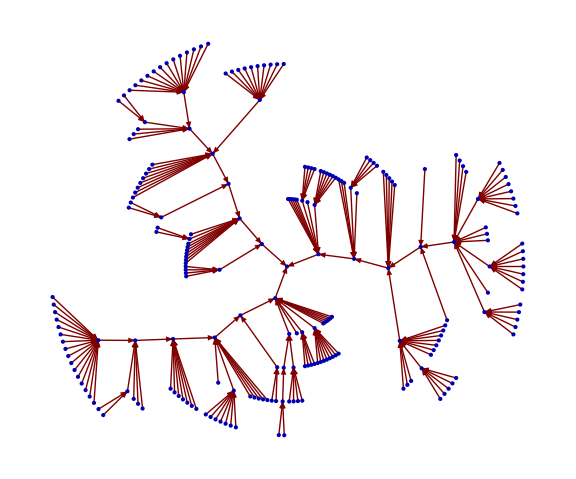

```mathematica
makeGraphWithLines[printNumberSteps[5000,5200]]
```

By visual inspection and some counting we see that all the numbers in the range 5000-5200 have sequences which terminate in 6174 (hover over nodes to see number!). Further, we can see that the largest number of iterations required was seven. 

We now compute the sequence from this routine for all 4 digit numbers and check to see that the after the seventh iteration the sequence has terminated in 6174. We see that this is only false for the numbers in which all digits are the same.

```mathematica
allNumberSeqs=printNumberSteps[1000,9999];
seventhIteration=Last[#]==6174&/@allNumberSeqs;
Extract[lst2,Position[seventhIteration,False]]
```

{{1111,0,0,0,0,0,0,0},{2222,0,0,0,0,0,0,0},{3333,0,0,0,0,0,0,0},{4444,0,0,0,0,0,0,0},{5555,0,0,0,0,0,0,0},{6666,0,0,0,0,0,0,0},{7777,0,0,0,0,0,0,0},{8888,0,0,0,0,0,0,0},{9999,0,0,0,0,0,0,0}}

Therefore, all sequences terminate in 6174 by the seventh iteration.